# 私の血糖値の推移

### 経緯

1月末に、かかりつけ医にて重度の糖尿病症状が確認され直ちに入院となった。
状態は重度の糖尿病性ケトアシドーシス（極度の脱水、栄養失調、ケトーシス状態、高血糖）。昏睡していてもおかしくない状態だったらしい。
2週間の入院。治療は脱水状態の離脱からはじめられ、数日後より栄養状態の回復治療、ついで糖尿病治療を行なった。同時に合併症検査が行われた。
結果的に合併症はなし、退院後はインスリンによる治療と定期的な通院検査を行うものとなった。

退院後の治療は食前のインスリン投与、1日1回の高濃度インスリン投与、カロリーコントロール、血糖コントロール、を行う。

血糖は血糖測定器があり随時測定可能。食事前に血糖測定を行なっている。

本日は血糖値の測定についてと血糖値の推移について報告する。

### 血糖値の測定

```mathematica
jpg="/Users/kouamano/Profile/IMG_0085.jpg"
```

/Users/kouamano/Profile/IMG_0085.jpg

下の写真が血糖値の測定器（左が測定器とチップ、右が穿刺具と穿刺針）。

血糖値の測定は、まず穿刺具にて指先に穿刺し、血液を測定器のチップに塗布する。数秒で結果が出る。

測定器には過去数十件の値と測定時間が記録されており、NFCによりスマホに転送可能。転送されたスマホ側でエクセルデータを作成しさらにメール転送が可能。

```mathematica
Import[jpg]
```

-Graphics-

### Data

スマホから転送されてきたデータのファイル。

```mathematica
dir="/Users/kouamano/Profile/"
```

/Users/kouamano/Profile/

```mathematica
xlsfile="01_24_2022-04_23_2022.xls"
```

01_24_2022-04_23_2022.xls

### Import

ファイルから値を読み取る。

```mathematica
importData=Import[dir<>xlsfile];
```

```mathematica
selectedData[1]=Transpose[Transpose[Drop[importData[[1]],1]][[{1,3}]]];
```

```mathematica
ts=TimeSeries[selectedData[1]]
```

TimeSeries[…]

単純なプロット。

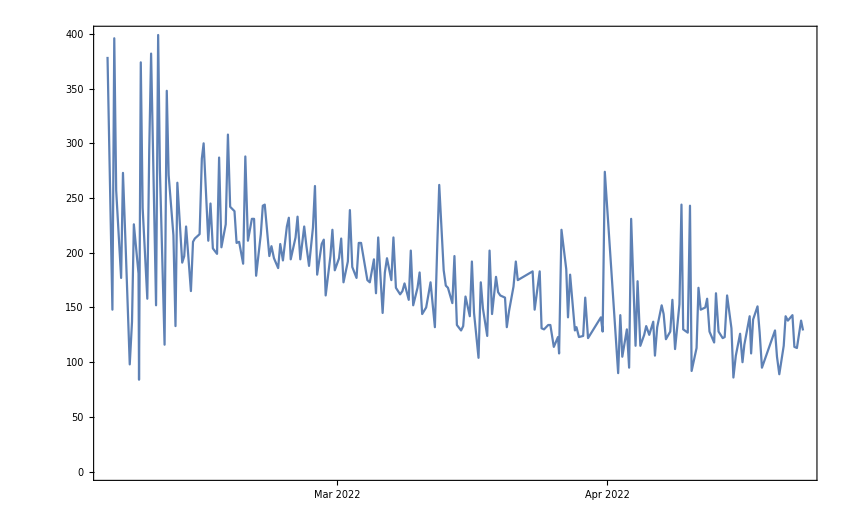

```mathematica
DateListPlot[ts]
```

### Interpolation

```mathematica
nts=Normal[ts];
```

```mathematica
nPts=Length[nts]
```

227

```mathematica
startDate=nts[[1,1]]
```

Wed 2 Feb 2022 16:45:00GMT+9

```mathematica
startTime=AbsoluteTime[nts[[1,1]]]
```

3852809100

```mathematica
endDate=nts[[-1,1]]
```

Sat 23 Apr 2022 11:53:00GMT+9

```mathematica
endTime=AbsoluteTime[nts[[-1,1]]]
```

3859703580

```mathematica
period=(endTime-startTime)/nPts//N
```

30372.2

```mathematica
endDate-startDate
```

79.7972 days

```mathematica
nPts/(endDate-startDate)
```

2.84471 per day

period 1

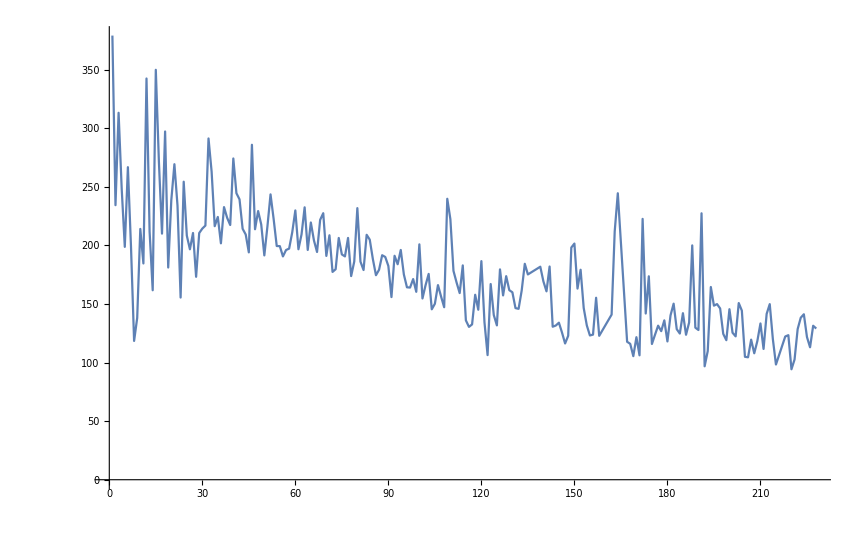

```mathematica
ListLinePlot[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]
```

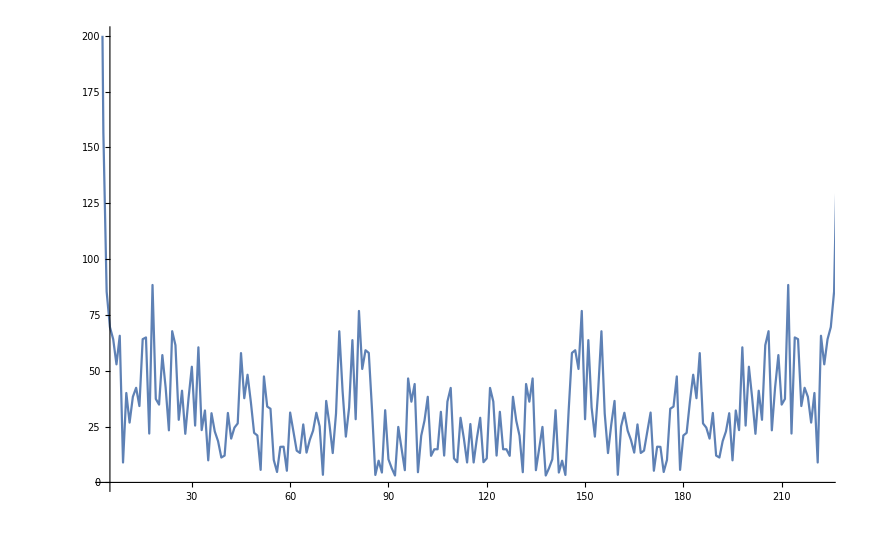

```mathematica
ListLinePlot[Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]//Abs,PlotRange->{{5,nPts-5},{0,200}}]
```

```mathematica
af=Abs[Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]];
```

```mathematica
max=Max[af[[5;;nPts-5]]]
```

88.4226

```mathematica
Position[af,max]
```

{{18},{212}}

```mathematica
(endTime-startTime)/60/60/24/17//N
```

4.69395

period 2

```mathematica
period2=(endTime-startTime)/(endDate-startDate)[[1]]/4 (*1日4回*)
```

21600.

```mathematica
nPts2=(endTime-startTime)/period2
```

319.189

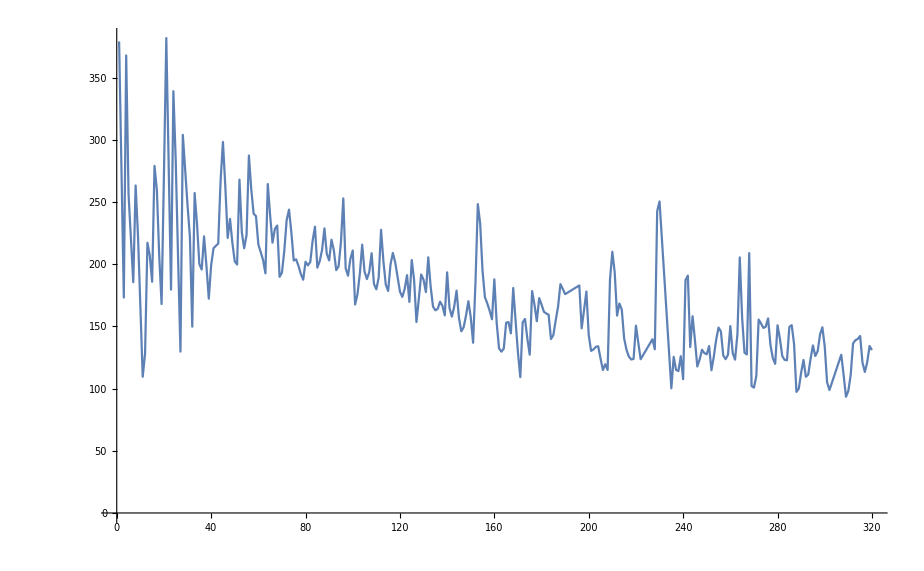

```mathematica
ListLinePlot[Table[Interpolation[ts][t],{t,startTime,endTime,period2}]]
```

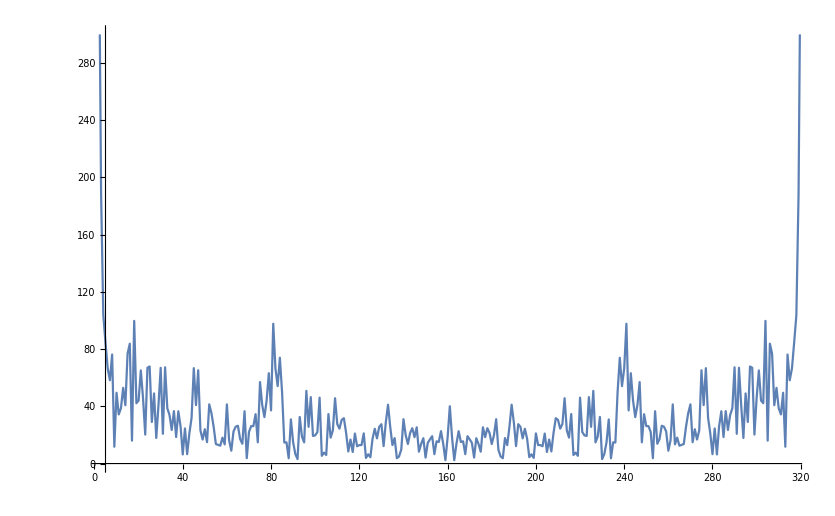

```mathematica
ListLinePlot[Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period2}]]//Abs,PlotRange->{{5,nPts2-5},{0,300}}]
```

### SemanticImport

```mathematica
semanticData=SemanticImport[dir<>xlsfile]
```

```mathematica
semantic["date","glu"]=Map[{#[[1]],#[[3]]}&,semanticData]
```

```mathematica
semantic["date"]=Map[#[[1]]&,semanticData]
```

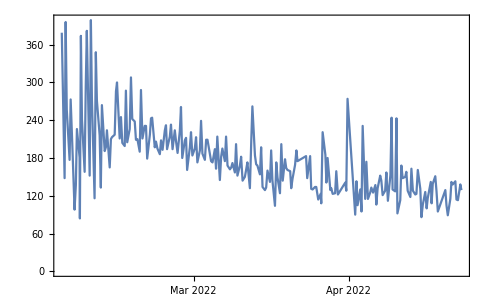

```mathematica
DateListPlot[semantic["date","glu"]]
```

```mathematica
semantic["date"]
```

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
AbsoluteTime[semantic["date"][[1]]]
```

3852809100

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
AbsoluteTime[semantic["date"]]
```

AbsoluteTime::arg: 引数Dataset[«227»]は日付または時間入力として解釈することができません．

AbsoluteTime[]